# shoving model

### data

```mathematica
p0s={3.85,3.825,3.80};
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022}};
```

```mathematica
tauAlpha={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3}};
```

```mathematica
gp={{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031}};
```

```mathematica
bulkModulusNumerical={{5.101213261152058,4.122334578970409,3.605284047837944,2.9468670767287946,2.758782392105095,2.4869350613165175,2.3823229832700057,2.145791131446564,2.04401759755755,2.0172074175350327,2.012965987189936,2.0071304906940655,2.0087451397548337,2.006949742477789,2.0083301028046394,2.0093425486609133,2.004879861430359},{5.899939133138476,5.317727656544852,5.082308251917092,4.37203397193947,3.793081807856936,3.5180079221904745,3.238231117069072,2.993221883595727,2.6825784698982194,2.500411026577562,2.3013062274523723,2.149647560090987,2.0499729805567375,1.8016100039092355,1.61424018782113,1.716199933682341},{5.954877584737085,5.526360771484304,5.343214629768459,5.067030747040075,4.54582986115226,3.7715610963749526,3.346419859597971,2.7908393694504205,2.255425252035912,1.7339725155163999,1.4414843998544193,1.5611622292251475,1.7359715666134266,1.8468038824630695}};
```

```mathematica
bulkModulusPeri={{3.1327868264012793,2.146669679594135,1.625445274825759,0.9613447767457817,0.7708497810237818,0.49584760259221594,0.3896030453314479,0.14924549774367601,0.045367576364034615,0.017862914323601802,0.013366041456455355,0.00727435539984978,0.008808819267151232,0.007044538150156038,0.008378659397645332,0.009381521318033909,0.004916821772182463},{3.9235712490701955,3.34492964624597,3.1090866508401844,2.394355999351477,1.81350140799965,1.5372789312579487,1.2562339007358252,1.0098889800876314,0.697893661877171,0.5144012690755295,0.31436160117244083,0.16183413459527374,0.05992257043973409,-0.1895833548666876,-0.37799115694107793,-0.2784861412942186},{3.9845466836681,3.5530111069355526,3.3680861484574054,3.092336863122748,2.56849555108396,1.7945904545591598,1.3708111421703097,0.8165136813594182,0.28331545146936116,-0.23555257510001448,-0.5267191387567112,-0.4094907539634249,-0.23833051629748753,-0.1305220947298187}};
```

```mathematica
blueGraient=Flatten[Table[{RGBColor[0.5,0.7,1,0.6],RGBColor[0.3,0.5,0.8,0.6],RGBColor[0,0.1,0.5,0.6]},{i,4}]]
```

{RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6],RGBColor[0.5, 0.7, 1, 0.6],RGBColor[0.3, 0.5, 0.8, 0.6],RGBColor[0, 0.1, 0.5, 0.6]}

```mathematica
redGraient=Flatten[Table[{RGBColor[1,0.2,0.3,0.6],RGBColor[0.8,0.1,0.1,0.6],RGBColor[0.5,0,0,0.6]},{i,4}]]
```

{RGBColor[1, 0.2, 0.3, 0.6],RGBColor[0.8, 0.1, 0.1, 0.6],RGBColor[0.5, 0, 0, 0.6],RGBColor[1, 0.2, 0.3, 0.6],RGBColor[0.8, 0.1, 0.1, 0.6],RGBColor[0.5, 0, 0, 0.6],RGBColor[1, 0.2, 0.3, 0.6],RGBColor[0.8, 0.1, 0.1, 0.6],RGBColor[0.5, 0, 0, 0.6],RGBColor[1, 0.2, 0.3, 0.6],RGBColor[0.8, 0.1, 0.1, 0.6],RGBColor[0.5, 0, 0, 0.6]}

## testing

```mathematica
niceStretchedExpStartEnd={{1,8},{1,14},{1,10}}
```

{{1,8},{1,14},{1,10}}

```mathematica
gpfit=NonlinearModelFit[Flatten[Table[Table[{gp[[p,T,1]]/(temperatures[[p,T]]^1.2),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],1],Exp[a x+b],{a,b},x]
```

FittedModel[…]

```mathematica
gpfit["BestFitParameters"]
```

{a→0.193353,b→-1.06662}

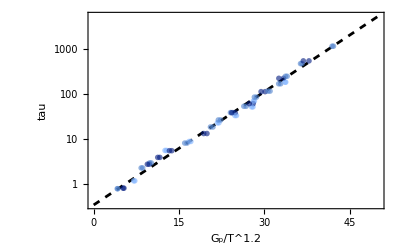

```mathematica
bulkModulusIncludePlot=Show[LogPlot[gpfit[x],{x,0,50},PlotStyle->{Dashed,Black},FrameLabel->{"G_p/T^1.2 ","tau"},LabelStyle->Directive[FontSize->12,FontName->"Arial"]],ListLogPlot[Table[Table[{gp[[p,T,1]]/(temperatures[[p,T]]^1.2),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm1[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->400,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->False],ListLogPlot[Table[Table[{1/(temperatures[[p,T]]^1.2*(1/gp[[p,T,1]]+1/(gp[[p,T,1]]+bulkModulusNumerical[[p,T]]))),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm1[4,redGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->400,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->False]]
```

```mathematica
Export["/home/chengling/Research/updates/09062024/shovingModel.jpeg",bulkModulusIncludePlot,ImageResolution->400]
```

/home/chengling/Research/updates/09062024/shovingModel.jpeg

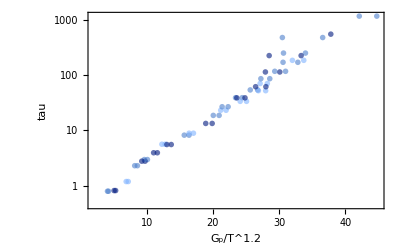

```mathematica
Show[ListLogPlot[Table[Table[{gp[[p,T,1]]/(temperatures[[p,T]]^1.2),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm1[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->400,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->False],ListLogPlot[Table[Table[{1/(temperatures[[p,T]]^1.2*(1/gp[[p,T,1]]+1/(gp[[p,T,1]]+bulkModulusPeri[[p,T]]))),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm1[4,redGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->400,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->False]]
```

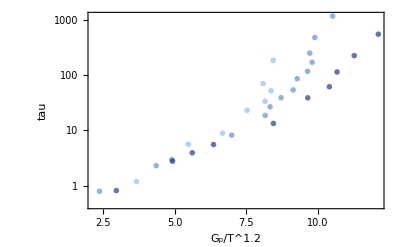

```mathematica
shovingPlot=Show[ListLogPlot[Table[Table[{1/(temperatures[[p,T]]*(1/gp[[p,T,1]]+1/(gp[[p,T,1]]+bulkModulusNumerical[[p,T]]))),tauAlpha[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm1[4,redGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->400,LabelStyle->Directive[FontSize->14],Joined->False]]
```

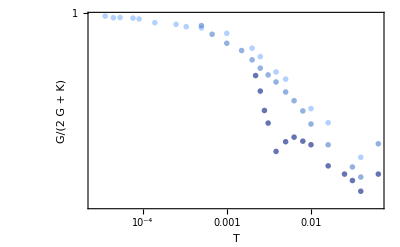

```mathematica
factorPlot=ListLogLogPlot[Table[Table[{temperatures[[p,T]],1-gp[[p,T,1]]/(2*gp[[p,T,1]]+bulkModulusNumerical[[p,T]])},{T,Length[temperatures[[p]]]}],{p,3}],LabelStyle->Directive[FontSize->12,FontName->"Arial"],PlotLegends->Table["p0="<>ToString[p0s[[p]]],{p,3}],PlotMarkers->pm1[4,redGraient],PlotStyle->blueGraient,FrameLabel->{"T ","G/(2  G + K)"},ImageSize->400,LabelStyle->Directive[FontSize->14],Joined->False]
```

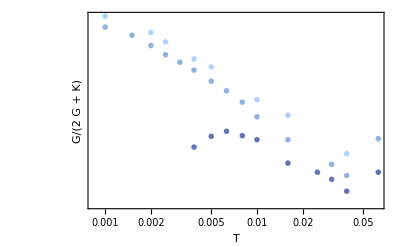

```mathematica
ListLogLogPlot[Table[Table[{temperatures[[p,T]],1-gp[[p,T,1]]/(2*gp[[p,T,1]]+bulkModulusNumerical[[p,T]])},{T,niceStretchedExpStartEnd[[p,2]]}],{p,3}],LabelStyle->Directive[FontSize->14,FontName->"Arial"],PlotMarkers->pm1[4,redGraient],PlotStyle->blueGraient,FrameLabel->{"T ","G/(2  G + K)"},ImageSize->400,PlotLegends->Table["p0="<>ToString[p0s[[p]]],{p,3}],LabelStyle->Directive[FontSize->5],Joined->False]
```

```mathematica
Export["/home/chengling/Research/updates/09062024/factorPlot.jpeg",factorPlot,ImageResolution->400]
```

/home/chengling/Research/updates/09062024/factorPlot.jpeg

```mathematica
Export["/home/chengling/Research/updates/09062024/shovingPlot.jpeg",shovingPlot,ImageResolution->400]
```

/home/chengling/Research/updates/09062024/shovingPlot.jpeg